```mathematica
alpha:=1/137;Mz:=92;thetaw:=0.23120;
F1:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.254,0.217,x];F2:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.333,0.054,x];F3:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][-0.340,-0.108,x];F4:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.010,-0.108,x];F5:=Function[{kaa,kgg,lambda},8*(kgg/kaa)^2*alpha/12*Mz^5*thetaw*kaa^2*1/lambda^2][0.095,0.217,x];
```

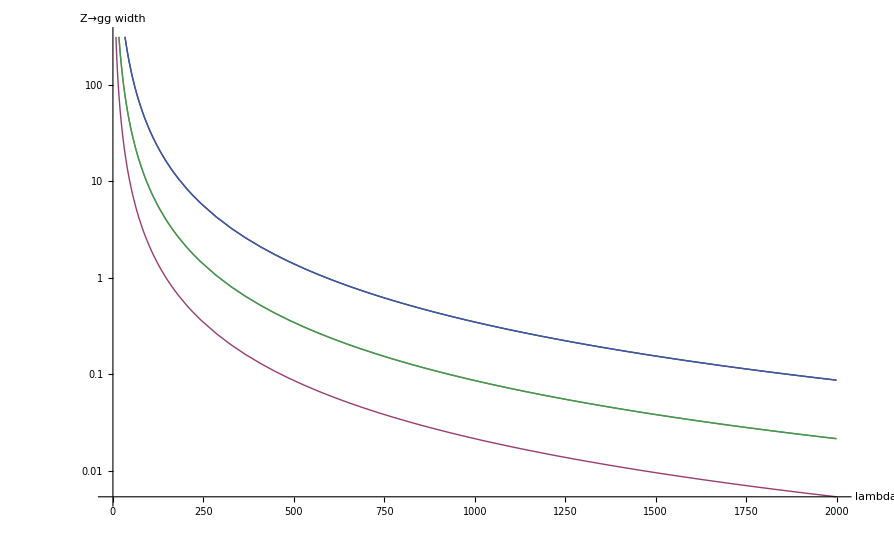

```mathematica
LogPlot[{F1,F2,F3,F4,F5},{x,0,2000},AxesLabel->{"lambda","Z→gg  width"}]
```

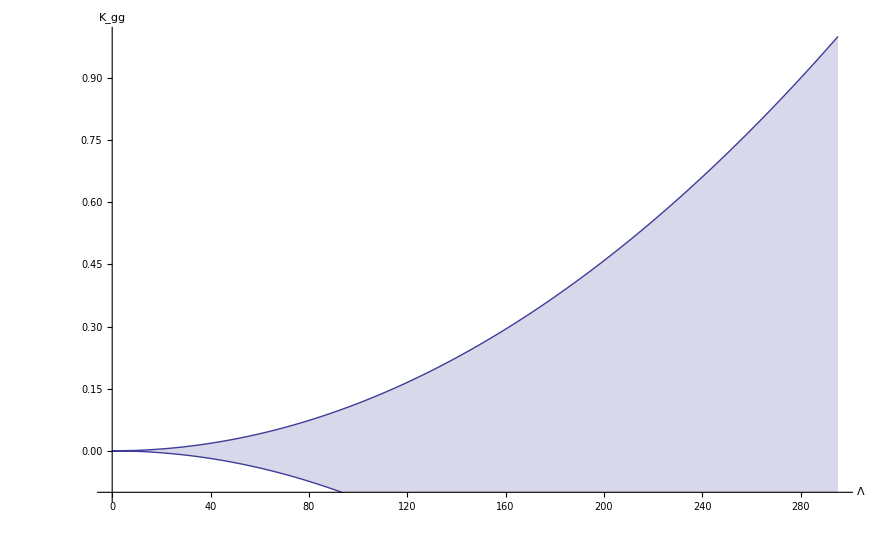

```mathematica
sinwb2:=0.23120;mz:=91.1876;alpha:=1/128;width:=0.001;
lambda:=Function[{kgg},(8/12*(kgg^2)*alpha*(mz^5)*sinwb2*1/width)^(1/4)][kgg];
ListPlot[Table[{lambda,kgg},{kgg,-0.1,1,0.001}],AxesLabel->{Λ,Subscript[K,gg]},Filling->Axis,Joined->True,AxesStyle->Directive[Black,20],AxesOrigin->{0,-0.1}]
```

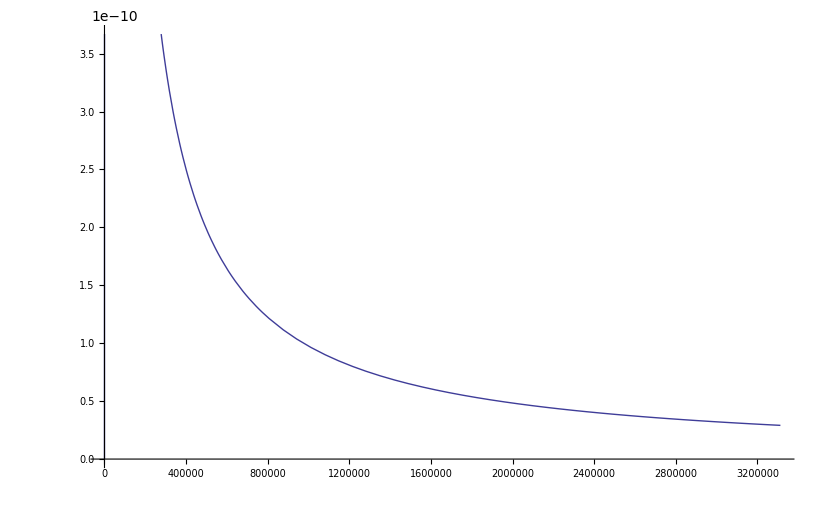

```mathematica
Zwidthfull:=2.4952;Zwidthfracmu:=0.03366;Zwidthfracuc:=0.101;Zwidthfracdsb:=0.166;Zmass:=91.1876;
Plot[12*Pi/Zmass^2 * Zwidthfracmu*Zwidthfracuc*s*Zwidthfull^2/((s-Zmass^2)^2 + s^2*Zwidthfull^2/Zmass^2),{s,0,1820^2}]
```

```mathematica
alphazmass:=1/128;sinw:=0.480832611;cosw:=0.876740947;Kgg:=0.2;
```

```mathematica
lambda:=200;Plot[32*Pi/12*sinw^2/(sinw^2*cosw^2)*alphazmass^2*(1/2-(2/3)*sinw^2)^2*Kgg^2*s/lamdba^4,{s,0,1820^2}]
```

-Graphics-